```mathematica
trainingset = {1-> "A", 2->"A", 3.5->"B", 4->"B"};
c = Classify[trainingset]
```

ClassifierFunction[…]

```mathematica
c[2.4]
```

A

```mathematica
c[4.11111]
```

B

```mathematica
c[4.11111, "Probabilities"]
```

<|A→0.166667,B→0.833333|>

```mathematica
c[2.6, 4.111111, 5, "Probabilities"]
```

ClassifierFunction::nonopt: Options expected (instead of Probabilities) beyond position 2 in …. An option must be a rule or a list of rules.

ClassifierFunction[…][2.6,4.11111,5,Probabilities]

```mathematica
c[2.6, 4.111111, 5]
```

ClassifierFunction::nonopt: Options expected (instead of 5) beyond position 2 in …. An option must be a rule or a list of rules.

ClassifierFunction[…][2.6,4.11111,5]

```mathematica
c[{2.6, 4.111111, 5}, "Probabilities"]
```

{<|A→0.833333,B→0.166667|>,<|A→0.166667,B→0.833333|>,<|A→0.166667,B→0.833333|>}

```mathematica
Plot[c[x, "Probability"->A], {x, 0, 5}]
```

ClassifierFunction::ukwncl: Unknown class A.

General::stop: Further output of ClassifierFunction::ukwncl will be suppressed during this calculation.

-Graphics-

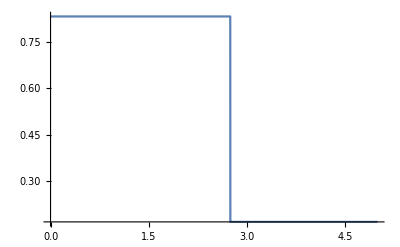

```mathematica
Plot[c[x, "Probability"->"A"], {x, 0, 5}]
```

```mathematica
Classify[trainingset, 2.6]
```

A

```mathematica
Classify[trainingset, 2.6, "Probabilities"]
```

<|A→0.0364496,B→0.96355|>

```mathematica
Classify[trainingset, 2.6]
```

B

```mathematica
c = Classify[{1.5, Blue}->"A", {3.2, Blue}->"A", {4.1, Red}->"B",
{5.3, Red}->"B", {10.,Green}->"C", {12.4, Red} ->"C"}]
```

Syntax::bktmcp: Expression "Classify[{1.5,Blue}→A,{3.2,Blue}→A,{4.1,Red}→B,{5.3,Red}→B,{10.,Green}→C,{12.4,Red}→C" has no closing "]".

```mathematica
c = Classify[{
{1.5, Blue}->"A", {3.2, Blue}->"A", {4.1, Red}->"B",
{5.3, Red}->"B", {10.,Green}->"C", {12.4, Red} ->"C"}]
```

ClassifierFunction[…]

```mathematica
c[{10.1, Blue}]
```

C

```mathematica
c[{10.1, Missing[]}]
```

C

```mathematica
c[{10.1, Blue}, "TopProbabilities"]
```

{C→0.6,B→0.2,A→0.2}

```mathematica
c = Classify[{"the cat is grey" -> -Graphics-, "my cat is fast" -> -Graphics-, "this dog is scary" -> -Graphics- , "the big dog" -> -Graphics-}]
```

ClassifierFunction[…]

```mathematica
c = classify[<|Red -> {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}, Green -> {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}, Blue -> {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}|>]
```

classify[<|RGBColor[1, 0, 0]→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},RGBColor[0, 1, 0]→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},RGBColor[0, 0, 1]→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>]

```mathematica
c = Classify[<|Red -> {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}, Green -> {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}, Blue -> {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}|>]
```

ClassifierFunction[…]

```mathematica
c[{-Graphics-, -Graphics-, -Graphics-}, {"Probability", Blue}]
```

{1.0823×10^-6,8.9928×10^-16,0.999979}

```mathematica
c = Classify[{{"butter", "sugar", "flour"}->"bad",
 {"flour", "butter"}->"good", {"tomato", "salt"}->"good"}]
```

ClassifierFunction[…]

```mathematica
c["butter"]
```

ClassifierFunction::mlincfttp: Incompatible variable type (NominalSequence) and variable value (butter).

ClassifierFunction[…][butter]

```mathematica
c[{"butter"}]
```

good

```mathematica
c[{"butter", "poison"}]
```

bad

```mathematica
c[{"poison"}, "Probabilities"]
```

<|bad→0.461531,good→0.538469|>

```mathematica
c[{"poison"}]
```

good

```mathematica
Characters["good"]
```

{g,o,o,d}

```mathematica
c[{"butter", "poison"}, "Probabilities"]
```

<|bad→0.524256,good→0.475744|>

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | NominalSequence
Classes | ,,badgood
Method | Markov
Accuracy | 100. % ± Indeterminate
Loss | 0.241 ± Indeterminate
Evaluation time | 1.07 ms/example
Classifier memory | 117. kB
Training examples used | 3 examples
Training time | 884. ms

```mathematica
cm = ClassifierMeasurements[c, {1.4->"A",5.3->"B",1.2->"B",4.6->"B",-3->"A"}]
```

ClassifierMeasurements::mlincfttp: Incompatible variable type (Nominal) and variable value ({A,B,B,B,A}).

ClassifierMeasurements[ClassifierFunction[…],{1.4→A,5.3→B,1.2→B,4.6→B,-3→A}]

```mathematica
c=Classify[{1,2,3.5,4,5}->{"A","A","A","B","B"}]
```

ClassifierFunction[…]

```mathematica
cm = ClassifierMeasurements[c, {1.4->"A",5.3->"B",1.2->"B",4.6->"B",-3->"A"}]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.8

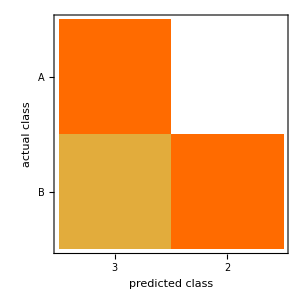

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
□(*Train on a dataset with missing features*)
```

□

```mathematica
c = Classify[{{2.3, "male"}->"A", {4.8, Missing[]}->"B", {Missing[], "female"}->"B",
{5.2, "female"}->"C",{Missing[], "male"}->"B",{1.3, "male"}->"A"}]
```

ClassifierFunction[…]

```mathematica
c[{1.2, "male"}]
```

A

```mathematica
c[{{1.2, Missing[]}, {Missing[], "female"}}]
```

{A,B}

```mathematica
d=Dataset[{<|"age"->32,"height"->160,"gender"->"female"|>,<|"height"->183,"age"->41,"gender"->"female"|>,<|"height"->123,"age"->30,"gender"->"female"|>,<|"height"->175,"age"->21,"gender"->"male"|>,<|"height"->150,"age"->11,"gender"->"male"|>,<|"age"->52,"height"->164,"gender"->"female"|>}]
```

Dataset[<>]

```mathematica
c = Classify[d->"gender"]
```

ClassifierFunction[…]

```mathematica
c[<|"height"->120, "age"->12->12|>]
```

ClassifierFunction::mlincfttp: Incompatible variable type (Numerical) and variable value (12→12).

```mathematica
c[<|"height"->120, "age"->12|>]ClassifierFunction[…][<|"height"->120,"age"->12->12|>]
```

General::noinfo: Input expression ClassifierFunction[…] contains insufficient information to interpret the result.

```mathematica
c[<|"height"->120, "age"->12|>]
```

female

```mathematica
ClassifierInformation[c, FeatureNames]
```

{age,height}

```mathematica
c[{12, 120}]
```

female

```mathematica
dnew=Dataset[{<|"height"->120,"age"->12|>,<|"height"->150,"age"->10|>,<|"height"->80,"age"->8|>}]
```

Dataset[<>]

```mathematica
c[dnew]
```

{female,male,female}

Create an artificial dataset from three normally distributed clusters :

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
sampledata[center_] := RandomVariate[MultinormalDistribution[center, IdentityMatrix[2], 200]
```

```mathematica
sampledata
```

```mathematica
sampledata[1]
```

sampledata[1]

```mathematica
clusters = sampledata /@ {{1.5, 1}, {-1.5, 1}, {0, -3}};
```

```mathematica
ListPlot[clusters, PlotStyle->Darker@{Yellow, Blue, Greed}]
```

Darker::arg: {RGBColor[1, 1, 0],RGBColor[0, 0, 1],Greed} should be a valid color directive, an image, or a list of them.

```mathematica
ListPlot[clusters, PlotStyle->Darker@{Yellow, Blue, Green}]-Graphics-
```

-Graphics- -Graphics-

```mathematica
sampledata[center_] := RandomVariate[MultinormalDistribution[center, IdentityMatrix[2]], 200];
```

```mathematica
clusters = sampledata /@ {{1.5, 1}, {-1.5, 1}, {0, -3}};
```

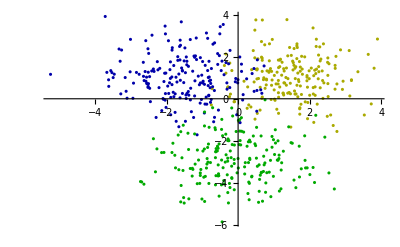

```mathematica
ListPlot[clusters, PlotStyle->Darker@{Yellow, Blue, Green}]
```

```mathematica
c = Classify[<|Yellow->clusters[[1]], Blue -> clusters[[2]], Green->clusters[[3]]|>]
```

ClassifierFunction[…]

```mathematica
clusters[[1]]
```

{{1.5243,1.79291},{-0.382523,1.58329},{0.253268,-0.453031},{0.904407,1.43653},{1.94762,-0.176549},{0.872367,1.80792},{2.49101,-0.836059},{0.467916,3.26836},{2.19008,1.40993},{1.94049,-0.948612},{2.51588,0.1045},{1.35022,1.4651},{0.617819,0.546908},{1.01833,-0.017931},{2.29414,0.523007},{2.76126,-1.55626},{3.34742,1.2864},{1.27376,0.17972},{1.7566,-0.26073},{0.37846,1.38657},{2.34903,1.32492},{2.09379,3.37291},{2.657,-1.27198},{2.21019,-0.256168},{1.53431,1.37233},{2.93302,0.836569},{1.03229,-0.0735077},{1.06109,0.706895},{1.98734,0.955869},{1.64432,0.643494},{1.13093,1.48528},{2.18625,2.83591},{0.554751,1.90159},{1.08178,-0.499649},{2.15339,0.1637},{0.795326,0.898011},{2.7131,1.44877},{3.16691,0.903011},{0.56973,0.965085},{1.57651,0.371268},{1.28039,0.759428},{1.9254,1.10326},{2.53922,1.66769},{0.652963,2.72393},{3.89326,2.84367},{3.63566,2.1131},{1.98411,1.33081},{0.526773,0.945203},{-0.724622,0.481789},{0.949813,0.892882},{1.92256,0.856194},{1.72712,-0.42855},{2.38402,2.61428},{1.39258,0.958238},{1.93772,0.55146},{0.472625,-0.970323},{2.50749,1.11423},{2.18139,2.49133},{2.71054,1.59015},{1.12482,0.87166},{2.31214,1.89055},{0.936127,1.3042},{1.27261,1.43171},{1.79642,1.16747},{2.15125,0.567723},{2.39627,0.756778},{2.76077,0.705409},{1.30084,0.748834},{1.59018,0.225062},{1.08915,1.2651},{1.71351,1.77109},{0.664576,0.0171125},{1.66834,0.0948005},{1.56434,2.39118},{1.25759,0.272614},{2.0983,0.532934},{0.786166,0.659902},{1.58833,1.45397},{1.28701,1.32187},{2.50842,0.721848},{-0.747882,-0.292098},{1.25848,0.254195},{-0.113075,-0.142198},{0.876216,1.33056},{1.12606,1.84182},{2.11313,1.09879},{0.423458,2.2943},{1.43866,2.44274},{0.357836,-0.390854},{1.11758,0.705201},{2.58565,-0.77304},{2.10154,0.227},{2.37067,0.0180594},{1.46252,0.236731},{3.10374,2.29537},{0.934526,0.642284},{1.34804,0.646622},{1.64055,1.91235},{1.61809,0.228495},{2.91453,0.446275},{-0.323107,1.75387},{0.298266,-0.291719},{1.38744,2.04414},{2.507,1.94497},{0.861219,1.26098},{0.67489,1.83278},{2.3611,0.8688},{1.66839,1.22284},{-0.340065,1.21903},{0.753812,0.497019},{3.1665,0.870238},{1.01257,1.1116},{1.4863,2.06576},{3.79921,1.45521},{1.5597,1.59339},{2.25107,1.53087},{1.00807,0.422184},{1.7745,2.02253},{3.52612,-0.773326},{0.0263184,-1.09888},{-0.232044,1.70049},{1.13218,0.0734235},{2.29203,1.80145},{1.86059,1.99545},{1.92624,1.02797},{1.16339,1.53035},{0.673496,1.30544},{2.28148,2.46973},{0.708832,0.910643},{2.14033,1.36159},{0.677349,3.75035},{-0.342041,2.13229},{2.25612,1.28859},{1.54187,1.72133},{1.59748,0.959957},{3.7195,-0.245902},{2.73415,2.0196},{1.72327,-0.732663},{0.95539,2.82567},{1.64491,2.61479},{0.534989,1.42463},{1.73929,0.60969},{2.11434,-1.12465},{1.38631,0.266301},{1.1265,0.287912},{0.466904,1.94897},{0.447339,0.800397},{-0.100533,-0.135786},{0.496241,3.75512},{0.672462,1.93661},{-0.280128,0.568601},{1.21674,1.12343},{1.99988,0.167036},{-0.240418,0.0973167},{1.36444,3.76811},{0.718327,0.999259},{1.7699,0.204227},{1.45876,0.739129},{1.69678,0.821832},{2.86124,2.32882},{1.61159,1.52673},{0.613916,-0.539991},{1.33585,1.01287},{2.23844,0.951105},{1.16834,1.83943},{0.791829,0.934524},{1.16376,0.561696},{-0.174371,1.3438},{1.68646,0.912133},{1.87581,-0.146342},{2.70801,0.456876},{0.526957,1.37444},{1.72056,-0.477609},{0.807646,1.32941},{1.13011,-0.693227},{2.04449,1.46121},{1.4731,-1.34873},{0.87667,2.61724},{1.22884,1.7383},{1.73643,1.31179},{1.18425,1.88266},{0.267624,0.563518},{1.7387,1.50976},{3.12152,0.133593},{0.92307,-0.0334776},{0.508664,1.39938},{0.536109,-0.695038},{2.50019,1.73487},{0.744208,2.56914},{2.24755,2.08083},{-0.213006,0.223008},{1.79034,1.41473},{0.165457,0.83553},{0.654324,1.98215},{1.65384,2.44014},{2.17005,1.19946},{1.64163,2.5195},{-0.295642,0.529164},{0.67604,0.0817816},{1.42665,0.299095}}

```mathematica
Show[
Plot3D[{
c[{x, y}, "Probability"->Yellow],
c[{x, y}, "Probability"->Blue], 
c[{x, y}, "Probability"-> Green]},
{x, -4, 4}, {y, -5, 4}, Exclusions->None,
ListPointPlot3D[Map[Append[#, 1]&, clusters, {2}, PlotStyle->{Yellow, Blue, Green}]]
```

```mathematica
Show[
Plot3D[{
c[{x, y}, "Probability"->Yellow],
c[{x, y}, "Probability"->Blue], 
c[{x, y}, "Probability"-> Green]},
{x, -4, 4}, {y, -5, 4}, Exclusions->None],
ListPointPlot3D[Map[Append[#, 1]&, clusters, {2}], PlotStyle->{Yellow, Blue, Green}]]
```

-Graphics3D-

```mathematica
Classify["Language", "the house is blue"]
```

English

```mathematica
Classify["Language","the house is blue, la maison est bleue","TopProbabilities"]
```

{French→0.707834,English→0.292036}

```mathematica
Classify["Language",{"What is this language?","¿Qué idioma es ese?","Quelle est cette langue?"},ClassPriors-><|Entity["Language","English"]->0.5,Entity["Language","Spanish"]->0.5|>]
```

{English,Spanish,Spanish}

```mathematica
Classify["FacebookTopic", "I love eating carrots in the morning"]
```

FoodAndDrink

```mathematica
Classify["FacebookTopic",{"I bought a new computer","happy birthday!","this skirt looks nice"}]
```

{Technology,SpecialOccasions,Fashion}

```mathematica
Classift["FacebookTopic", {"what is this topic?", "wdsfsdfsfsdffds"}]
```

Classift[FacebookTopic,{what is this topic?,wdsfsdfsfsdffds}]

```mathematica
Classify["FacebookTopic", {"what is this topic?", "wdsfsdfsfsdffds"}]
```

{Indeterminate,Indeterminate}

```mathematica
Classify["CountryFlag", {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

{Brazil,Germany,United States,Canada,Mexico}

```mathematica
Classify["NameGender", {"Tom", "Stacy", "John", "Natalie"}]
```

{Male,Female,Male,Female}

```mathematica
Classify["NotablePerson", -Graphics-]
```

Albert Einstein

```mathematica
Classify["Sentiment", {"I love this movie", "I am so sad", "My phone broke again"}]
```

{Positive,Negative,Negative}

```mathematica
Classify["Profanity", Import["http://www.urbandictionary.com/random.php"]]
```

True

```mathematica
Classify["Profanity", Import["http://www.urbandictionary.com/random.php"]]
```

True

```mathematica
Classify["Profanity", Import["http://www.urbandictionary.com/random.php"]]
```

True

```mathematica
Classify["Spam","Dear recipient,*** Technologies announces the beginning of a new unprecendented global employment campaign.reviser yeller winers butchery twenties
 Due to company's exploding growth *** is expanding business to the European region.During last employment campaign over 1500 people worldwide took part in ***'s business
 and more than half of them are currently employed by the company.And now we are offering you
 one more opportunity to earn extra money working with *** Technologies.druggists blame classy gentry Aladdin
 
We are looking for honest,responsible,hard-working people that can dedicate 2-4 hours of their
 time per day and earn extra Â$300-500 weekly.All offered positions are currently part-time
 and give you a chance to work mainly from home.lovelies hockey Malton meager reordered
 
Please visit ***'s corporate web site (http://www.***.com/sta/home/0077.htm) for more details regarding these vacancies."]
```

True

```mathematica
data = {1->True, 2->True, 3-> True, 4 -> True, 5-> False, 6-> True};
```

```mathematica
c = Classify[data]
```

ClassifierFunction[…]

```mathematica
c[5]
```

```mathematica
Truec[5, "Probabilities"]
```

Truec[5,Probabilities]

```mathematica
c[5, "Probabilities"]
```

<|False→0.430723,True→0.569277|>

```mathematica
c[5, ClassPriors-><|False->0.5, True ->0.5|>]
```

False

```mathematica
c[5, "Probabilities", ClassPriors-><|False->0.5, True ->0.5|>]
```

<|False→0.694175,True→0.305825|>

```mathematica
c=Classify[data,ClassPriors-><|False->0.5,True->0.5|>]
```

ClassifierFunction[…]

```mathematica
c[5]
```

False

```mathematica
c[5, "Probabilities"]
```

<|False→0.694175,True→0.305825|>

```mathematica
c[5, ClassPriors -> <|False -> 0.2, True -> 0.8 |>]
```

True

```mathematica
dataset = {{1.4, "A"}, {1.5, "A"}, {2.3, "B"}, {5.4, "B"}};
```

```mathematica
fe = FeatureExtraction[dataset]
```

FeatureExtractorFunction[…]

```mathematica
Classify[dataset->{"Yes", "No", "No", "No"}, FeatureExtractor->fe]
```

ClassifierFunction[…]

```mathematica
fe
```

FeatureExtractorFunction[…]

```mathematica
c = Classify[{"The cat is grey." -> -Graphics-, "My cat is fast." -> -Graphics-, "This dog is scary." -> -Graphics- , "The big dog." -> -Graphics-}, 
  FeatureExtractor -> {ToUpperCase, RemoveDiacritics, 
    "SegmentedWords"}]
```

ClassifierFunction[…]

```mathematica
c[{"Nice CAT","What a dög"}]
```

{-Graphics-,-Graphics-}

```mathematica
c = Classify[{
{2.3, "male"}->"a",
{4.8, Missing[]}->"b",
{Missing[], "female"}->"a",
{5.2, "female"}->"b"}, FeatureNames-> {"age", "gender"}]
```

ClassifierFunction::mlincfttp: Incompatible variable type (Numerical) and variable value (age FeatureNames).

ClassifierFunction[…][{age FeatureNames,gender FeatureNames},BatchProcessing→Automatic,TieBreakerFunction→RandomChoice,ClassPriors→Automatic,IndeterminateThreshold→Automatic,PerformanceGoal→Automatic,RandomSeeding→1234,UtilityFunction→Automatic]

```mathematica
c[<|"age"->3.3, "gender"->"male"|>]
```

ClassifierFunction[…][{age FeatureNames,gender FeatureNames},BatchProcessing→Automatic,TieBreakerFunction→RandomChoice,ClassPriors→Automatic,IndeterminateThreshold→Automatic,PerformanceGoal→Automatic,RandomSeeding→1234,UtilityFunction→Automatic][<|age→3.3,gender→male|>]

```mathematica
c = Classify[{
{2.3, "male"}->"a",
{4.8, Missing[]}->"b",
{Missing[], "female"}->"a",
{5.2, "female"}->"b"}, FeatureNames-> {"age", "gender"}]
```

ClassifierFunction[…]

```mathematica
c[<|"age"->3.3, "gender"->"male"|>]
```

a

```mathematica
c[{3.3, "male"}]
```

a

```mathematica
c=Classify[{<|"age"->2.3,"gender"->"male"|>->"a",<|"age"->4.6|>->"b",<|"gender"->"female"|>->"a",<|"gender"->"female","age"->5.2|>->"b"},FeatureNames->{"gender","age"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c, FeatureNames]
```

{gender,age}

```mathematica
c[{"female", 6.5}]
```

b

```mathematica
c = Classify[{
{"butter", "sugar"}->"bad", 
{"flour", "butter"}->"good",
{"tomato", "salt"}->"good"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c, FeatureTypes]
```

<|f1→Text,f2→Text|>

```mathematica
c["butter", "tomato", "apple"]
```

ClassifierFunction::nonopt: Options expected (instead of apple) beyond position 2 in …. An option must be a rule or a list of rules.

ClassifierFunction[…][butter,tomato,apple]

```mathematica
c2 = Classify[{
{"butter", "sugar"}->"bad",
{"flour", "butter"}-> "good",
{"tomato", "salt"}->"good"}, FeatureTypes->"NominalSequence"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c2, FeatureTypes]
```

<|f1→NominalSequence|>

```mathematica
c2[{"butter", "tomato", "apple"}]
```

good

```mathematica
trainingset={<|"age"->32,"gender"->1|>->"tall",<|"age"->41,"gender"->2|>->"short",<|"age"->17,"gender"->2|>->"short",<|"age"->11,"gender"->1|>->"tall"};
```

```mathematica
c = Classify[trainingset]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c, FeatureTypes]
```

<|age→Numerical,gender→Numerical|>

```mathematica
c = Classify[trainingset, FeatureTypes-><|"gender"->"Nominal"|>]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c, FeatureTypes]
```

<|age→Numerical,gender→Nominal|>

```mathematica
c[5, "Probabilities"]
```

ClassifierFunction::mlbddataev: The data being evaluated is not formatted correctly.

ClassifierFunction[…][5,Probabilities]

```mathematica
data = {
1->"B", 
2->"B",
3->"A",
4->"B",
5->"A",
6->"A"
};
```

```mathematica
c = Classify[data, IndeterminateThreshold->0.9]
```

ClassifierFunction[…]

```mathematica
c[5, "Probabilities"]
```

<|A→0.666667,B→0.333333|>

```mathematica
c[5]
```

Indeterminate

```mathematica
c[5, IndeterminateThreshold->0.5]
```

A

```mathematica
traingingset = {1,2, 3, 4, 5, 6, 7}-> {"a", "a", "b", "a", "b", "b", "b"};
```

```mathematica
logistic = Classify[trainingset, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
rf = Classify[trainingset, Method ->"RandomForest"]
```

```mathematica
ClassifierFunction[…]
traingingset = {1,2, 3, 4, 5, 6, 7}-> {"a", "a", "b", "a", "b", "b", "b"};
```

General::noinfo: Input expression ClassifierFunction[…] contains insufficient information to interpret the result.

```mathematica
trainingset = {1,2, 3, 4, 5, 6, 7}-> {"a", "a", "b", "a", "b", "b", "b"};
```

```mathematica
logistic = Classify[trainingset, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
rf = Classify[trainingset, Method ->"RandomForest"]
```

ClassifierFunction[…]

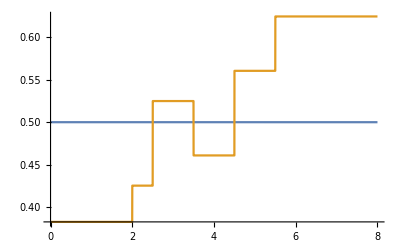

```mathematica
Plot[{
logistic[x, "Probability" -> "a"],
rf[x, "Probability"->"a"]
}, {x, 0, 8}, Exclusions->None]
```

```mathematica
Plot[{logistic[x,"Probability"->"a"],rf[x,"Probability"->"a"]},{x,0,8},Exclusions->None]
```

-Graphics-

```mathematica
trainingset={1,2,3,4,5,6,7}->{"a","a","b","a","b","b","b"};
```

```mathematica
logistic=Classify[trainingset,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
rf=Classify[trainingset,Method->"RandomForest"]
```

ClassifierFunction[…]

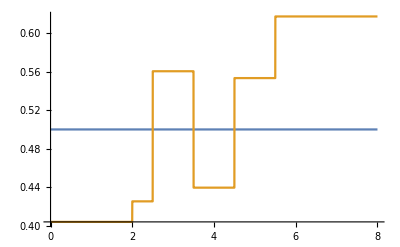

```mathematica
Plot[{logistic[x,"Probability"->"a"],rf[x,"Probability"->"a"]},{x,0,8},Exclusions->None]
```

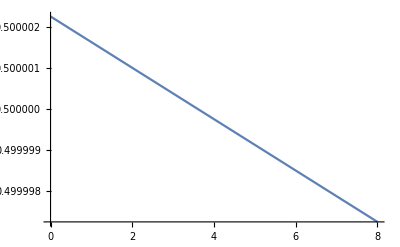

```mathematica
Plot[{logistic[x,"Probability"->"a"]},{x,0,8},Exclusions->None]
```

```mathematica
trainingset = ExampleData[{"MachineLearning", "UCILetter"}, "TrainingData"];
```

```mathematica
c1 = Classify[traingingset, Method->"NearestNeighbours"]
```

Classify::mlnasethl: "NearestNeighbours" is not an available method. Did you mean "NearestNeighbors" instead? Possible methods also include "DecisionTree", "GradientBoostedTrees", "LogisticRegression", "Markov", "NaiveBayes", "NeuralNetwork", "PriorBaseline", "RandomForest", "SupportVectorMachine", and Automatic.

```mathematica
Classify[{1,2,3,4,5,6,7}->{"a","a","b","a","b","b","b"},Method->"NearestNeighbors"]
```

ClassifierFunction[…]

```mathematica
c1 = Classify[traingingset, Method->"NearestNeighbors"]
```

ClassifierFunction[…]

```mathematica
testset = ExampleData[{"MachineLearning", "UCILetter"}, "TestData"];
```

```mathematica
ClassifierMeasurements[c1, testset, "Accuracy"]
```

ClassifierMeasurements::mlincfttp: Incompatible variable type (Numerical) and variable value ({4,10,6,7,9,9,6,4,3,6,7,7,9,8,5,6}).

ClassifierMeasurements[ClassifierFunction[…],{{4,10,6,7,9,9,6,4,3,6,7,7,9,8,5,6}→U,{6,9,8,4,3,8,7,3,4,13,5,8,6,8,0,8}→N,{6,9,8,8,10,7,7,5,4,7,6,8,7,9,7,10}→V,3994,{6,9,6,7,5,6,11,3,7,11,9,5,2,12,2,4}→T,{2,3,4,2,1,8,7,2,6,10,6,8,1,9,5,8}→S,{4,9,6,6,2,9,5,3,1,8,1,8,2,7,2,8}→A},Accuracy]
 |  |  |  |

```mathematica
trainingset=ExampleData[{"MachineLearning","UCILetter"},"TrainingData"];
c1=Classify[trainingset,Method->"NearestNeighbors"]
```

ClassifierFunction[…]

```mathematica
testset=ExampleData[{"MachineLearning","UCILetter"},"TestData"];
```

```mathematica
ClassifierMeasurements[c1,testset,"Accuracy"]
```

0.93925

```mathematica
c2=Classify[trainingset,Method->"NaiveBayes"]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[c2, testset, "Accuracy"]
```

0.73125

```mathematica
First[AbsoluteTiming[c1[testset[[All, 1]]]]]
```

3.43201

```mathematica
First[AbsoluteTiming[c2[testset[[All, 1]]]]]
```

0.877407

```mathematica
First[AbsoluteTiming[c1[testset[[All, 1]]]]]
```

3.66366

```mathematica
data = Map[#->Count[#, 1] == 1&,Tuples[{
{1, 2, 3}, {1, 2, 3}, {1, 2}, {1, 2, 3}, {1, 2, 3, 4}, {1, 2}}]];
```

```mathematica
trainingset = RandomSample[data, 169];
```

```mathematica
AssociationMap[ClassifierMeasurements[
Classify[trainingset, Method->#], data, "Accuracy"&,{"RandomForest",
"NaiveBayes", "SupportVectorMachine", "NearestNeighbours", "LogisticRegression"}]
```

```mathematica
AssociationMap[ClassifierMeasurements[
Classify[trainingset, Method->#], data, "Accuracy"]&,{"RandomForest",
"NaiveBayes", "SupportVectorMachine", "NearestNeighbors", "LogisticRegression"}]
```

<|RandomForest→0.787037,NaiveBayes→0.787037,SupportVectorMachine→0.787037,NearestNeighbors→0.763889,LogisticRegression→0.831019|>

```mathematica
traininset=ExampleData[{"MachineLearning", "Satellite"}, "TrainingData"];
c1 = Classify[trainingset, PerformanceGoal->"TrainingSpeed"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c, "TrainingTime"]
```

1.52087 s

```mathematica
testset = ExampleData[{"MachineLearning", "Satellite"}, "TestData"];
ClassifierMeasurements[c1, testset, "Accuracy"]
```

ClassifierMeasurements::mlbftlgth2: Example {80,102,102,79,76,102,102,79,76,102,106,83,76,99,108,85,76,103,118,88,80,107,118,88,79,107,109,87,79,107,109,87,79,107,113,87} should have 6 features instead of 36.

ClassifierMeasurements[ClassifierFunction[…],{{80,102,102,79,76,102,102,79,76,102,106,83,76,99,108,85,76,103,118,88,80,107,118,88,79,107,109,87,79,107,109,87,79,107,113,87}→gray soil,1998,{60,71,91,81,60,64,104,99,56,64,108,96,63,79,93,6,75,109,96,59,83,92,74,59,83,92,70,63,79,108,92}→30},Accuracy]
 |  |  |  |

```mathematica
c1=Classify[trainingset,PerformanceGoal->"TrainingSpeed"];
```

```mathematica
testset = ExampleData[{"MachineLearning", "Satellite"}, "TestData"];
ClassifierMeasurements[c1, testset, "Accuracy"]
```

ClassifierMeasurements::mlbftlgth2: Example {80,102,102,79,76,102,102,79,76,102,106,83,76,99,108,85,76,103,118,88,80,107,118,88,79,107,109,87,79,107,109,87,79,107,113,87} should have 6 features instead of 36.

ClassifierMeasurements[ClassifierFunction[…],{{80,102,102,79,76,102,102,79,76,102,106,83,76,99,108,85,76,103,118,88,80,107,118,88,79,107,109,87,79,107,109,87,79,107,113,87}→gray soil,1998,{60,71,91,81,60,64,104,99,56,64,108,96,63,79,93,6,75,109,96,59,83,92,74,59,83,92,70,63,79,108,92}→30},Accuracy]
 |  |  |  |

```mathematica
c2=Classify[trainingset]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c1, "TrainingTime"]
```

10.785 s

```mathematica
c2 = Classify[trainingset]
```

```mathematica
ClassifierFunction[…]
ClassifierInformation[c2, "Accuracy"]
```

General::noinfo: Input expression ClassifierFunction[…] contains insufficient information to interpret the result.

```mathematica
ClassifierFunction[…]
ClassifierMeasurements[c2, testset,"Accuracy"]
```

General::noinfo: Input expression ClassifierFunction[…] contains insufficient information to interpret the result.

```mathematica
trainingset=ExampleData[{"MachineLearning","Satellite"},"TrainingData"];
c2=Classify[trainingset];
ClassifierInformation[c2,"TrainingTime"]
ClassifierMeasurements[c2,testset,"Accuracy"]
```

19.2775 s

0.8925

```mathematica
c3=Classify[trainingset,PerformanceGoal->{"TrainingSpeed","Memory"}]
```

ClassifierFunction[…]

```mathematica
ByteCount/@{c2,c3}
```

{1648728,314936}

```mathematica
ClassifierMeasurements[c3,testset,"Accuracy"]
```

0.8365

```mathematica
c=Classify[{1,2,3,4}->{"A","A","B","B"},TimeGoal->5]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c, "TrainingTime"]
```

5.79365 s

```mathematica
dataset = ExampleData[{"MachineLearning", "Mushroom"}, "Data"];
```

```mathematica
c = Classify[dataset, TimeGoal->.1]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | Mixed (number: 22)
Classes | ,,ediblepoisonous
Method | LogisticRegression
Accuracy | 89. % ± 0.78 %
Loss | 0.651 ± 0.00076
Evaluation time | 53.5 µs/example
Classifier memory | 1.57 MB
Training examples used | 8124 examples
Training time | 15.4 s
 |

```mathematica
c = Classify[dataset, TimeGoal->5]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | Mixed (number: 22)
Classes | ,,ediblepoisonous
Method | DecisionTree
Accuracy | 99. % ± 0.71 %
Loss | 0.0322 ± 0.011
Evaluation time | 288. µs/example
Classifier memory | 1.58 MB
Training examples used | 8124 examples
Training time | 22.4 s
 |

```mathematica
dataset = ExampleData[{"MachineLearning", "UCILetter"}, "Data"];
```

```mathematica
Classify[dataset, TrainingProgressReporting->"Panel"];
Classify[dataset, TrainingProgressReporting->"SimplePanel"];
Classify[dataset, TrainingProgressReporting->"Print"];
```

|    |  Time elapsedTraining example usedCurrent best methodCurrent accuracyCurrent loss

|        |    8.6s20/20000DecisionTree0.04003.26

|        |    9.2s20/20000GradientBoostedTrees0.02113.26

|        |    9.8s100/20000LogisticRegression0.2203.09

|        |    10s100/20000NearestNeighbors0.3892.93

|        |    10s500/20000NearestNeighbors0.3892.93

|        |    15s500/20000GradientBoostedTrees0.5301.84

|        |    16s500/20000GradientBoostedTrees0.5301.84

|        |    17s3000/20000LogisticRegression0.7680.835

|        |    31s3000/20000LogisticRegression0.7680.835

|        |    32s3000/20000LogisticRegression0.7680.835

|        |    32s3000/20000LogisticRegression0.7680.835

|        |    33s3000/20000LogisticRegression0.7680.835

|        |    34s3000/20000LogisticRegression0.7680.835

|        |    35s3000/20000LogisticRegression0.7680.835

|        |    35s3000/20000LogisticRegression0.7680.835

|        |    36s3000/20000LogisticRegression0.7680.835

|        |    37s3000/20000LogisticRegression0.7680.835

|        |    37s3000/20000LogisticRegression0.7680.835

|        |    39s16000/20000NearestNeighbors0.9350.256

|        |    1m07s16000/20000NearestNeighbors0.9350.256

|        |    1m07s16000/20000NearestNeighbors0.9350.256

|        |    1m08s16000/20000NearestNeighbors0.9350.256

|        |    1m08s16000/20000NearestNeighbors0.9350.256

|        |    1m09s16000/20000NearestNeighbors0.9350.256

|        |    1m09s16000/20000NearestNeighbors0.9350.256

|        |    1m10s16000/20000NearestNeighbors0.9350.256

|        |    1m11s16000/20000NearestNeighbors0.9350.256

|        |    1m11s16000/20000NearestNeighbors0.9350.256

|        |    1m12s16000/20000NearestNeighbors0.9350.256

|        |    1m12s16000/20000NearestNeighbors0.9350.256

|        |    1m13s16000/20000NearestNeighbors0.9350.256

|        |    1m13s16000/20000NearestNeighbors0.9350.256

|        |    1m14s16000/20000NearestNeighbors0.9350.256

|        |    1m14s16000/20000NearestNeighbors0.9350.256

|        |    1m15s16000/20000NearestNeighbors0.9350.256

|        |    1m21s16000/20000NearestNeighbors0.9350.256

|        |    1m21s16000/20000NearestNeighbors0.9350.256

|        |    1m22s16000/20000NearestNeighbors0.9350.256

|        |    1m23s16000/20000NearestNeighbors0.9350.256

```mathematica
trainingset = {1, 2, 3, 4} -> {"yes", "yes", "no", "no"};
c1 = Classify[trainingset]
```

ClassifierFunction[…]

```mathematica
c1[2.55, "Probabilities"]
```

<|no→0.954545,yes→0.0454545|>

```mathematica
ClassifierInformation[c1, UtilityFunction]
```

<|no→<|no→1.,yes→0.,Indeterminate→0.|>,yes→<|no→0.,yes→1.,Indeterminate→0.|>|>

```mathematica
c2 = Classify[trainingset, UtilityFunction-><|"no"-><|"no"->1, 
"yes"-> 0|>, "yes"-> <|"no"->-10, "yes"->1|>|>]
```

ClassifierFunction[…]

```mathematica
c2[2.55, "Probabilities"]
```

<|no→0.954545,yes→0.0454545|>

```mathematica
c2[2.55]
```

no

```mathematica
c2 = Classify[trainingset, UtilityFunction-><|"no"-><|"no"->1, 
"yes"-> 0|>, "yes"-> <|"no"->-100, "yes"->1|>|>]
```

ClassifierFunction[…]

```mathematica
c2[2.55]
```

yes

```mathematica
c2[2.55,UtilityFunction-><|"no"-><|"no"->1,"yes"->0|>,"yes"-><|"no"->0,"yes"->1|>|>]
```

no

```mathematica
trainingset = ExampleData[{"MachineLearning", "FisherIris"}, "TrainingData"];
```

```mathematica
c1 = Classify[traingingset, Method -> "LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
trainingset=ExampleData[{"MachineLearning","FisherIris"},"TrainingData"];
c1=Classify[trainingset,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c1, "L2Regularization"]
```

1.

```mathematica
validationset = ExampleData[{"MachineLearning", "FisherIris"}, "TestData"][[;;10]];
c2 = Classify[trainingset, ValidationSet->validationset, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c2, "L2Regularization"]
```

0.01

```mathematica
digit = Classify[
  {-Graphics- -> 2, -Graphics- -> 5, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 2, -Graphics- -> 7, -Graphics- -> 5, -Graphics- -> 1, -Graphics- -> 3, -Graphics- -> 0, -Graphics- -> 3, -Graphics- -> 9, -Graphics- -> 6, -Graphics- -> 2, -Graphics- -> 8, -Graphics- -> 2, -Graphics- -> 0, -Graphics- -> 6, -Graphics- -> 6, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 7, -Graphics- -> 8, -Graphics- -> 5, -Graphics- -> 0, -Graphics- -> 4, -Graphics- -> 7, -Graphics- -> 6, -Graphics- -> 0, -Graphics- -> 2, -Graphics- -> 5, -Graphics- -> 3, -Graphics- -> 1, -Graphics- -> 5, -Graphics- -> 6, -Graphics- -> 7, -Graphics- -> 5, -Graphics- -> 4, -Graphics- -> 1, -Graphics- -> 9, -Graphics- -> 3, -Graphics- -> 6, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 9, -Graphics- -> 3, -Graphics- -> 0, -Graphics- -> 3, -Graphics- -> 7, -Graphics- -> 4, -Graphics- -> 4, -Graphics- -> 3, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 4, -Graphics- -> 1, -Graphics- -> 3, -Graphics- -> 7, -Graphics- -> 6, -Graphics- -> 4, -Graphics- -> 7, -Graphics- -> 2, -Graphics- -> 7, -Graphics- -> 2, -Graphics- -> 5, -Graphics- -> 2, -Graphics- -> 0, -Graphics- -> 9, -Graphics- -> 8, -Graphics- -> 9, -Graphics- -> 8, -Graphics- -> 1, -Graphics- -> 6, -Graphics- -> 4, -Graphics- -> 8, -Graphics- -> 5, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 6, -Graphics- -> 7, -Graphics- -> 4, -Graphics- -> 5, -Graphics- -> 8, -Graphics- -> 4, -Graphics- -> 3, -Graphics- -> 1, -Graphics- -> 5, -Graphics- -> 1, -Graphics- -> 9, -Graphics- -> 9, -Graphics- -> 9, -Graphics- -> 2, -Graphics- -> 4, -Graphics- -> 7, -Graphics- -> 3, -Graphics- -> 1, -Graphics- -> 9, -Graphics- -> 2, -Graphics- -> 9, -Graphics- -> 6}]
```

ClassifierFunction[…]

```mathematica
digit[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

{0,1,2,3,4,1,0,7,6,9}

```mathematica
digit[-Graphics-, "TopProbabilities"]
```

```mathematica
{0->0.37744429069236346,4->0.3730188271127285,6->0.14359140706073473,2->0.05406991583377087,5->0.04251059322208816}
```

```mathematica
1+1
```

2

```mathematica
c = Classify[ExampleData[{"MachineLearning", "FisherIris"}, "TrainingData"]]
```

ClassifierFunction[…]

```mathematica
c[{4.3, 3.1, 1.2, 0.3}]
```

setosa

```mathematica
cm = ClassifierMeasurements[c, ExampleData[{"MachineLearning", "FisherIris"}, "TestData"]]
```

ClassifierMeasurementsObject[…]

```mathematica
cm ["Accuracy"]
```

0.955556

```mathematica
cm["confusionMatricPlot"]
```

ClassifierMeasurementsObject::mlnaseth: "confusionMatricPlot" is not an available property. Did you mean "ConfusionMatrixPlot" instead?

```mathematica
cm["confusionMatrixPlot"]ClassifierMeasurementsObject[…]["confusionMatricPlot"]
```

General::noinfo: Input expression ClassifierMeasurementsObject[…] contains insufficient information to interpret the result.

```mathematica
cm["ConfusionMatrixPlot"]ClassifierMeasurementsObject[…]["confusionMatricPlot"]
```

General::noinfo: Input expression ClassifierMeasurementsObject[…] contains insufficient information to interpret the result.

```mathematica
cm=ClassifierMeasurements[c,ExampleData[{"MachineLearning","FisherIris"},"TestData"]]
```

ClassifierMeasurementsObject[…]

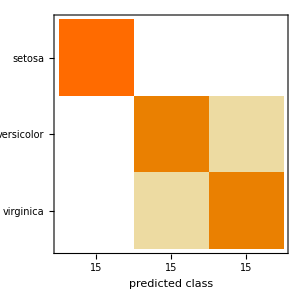

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
dataset = ExampleData[{"MachineLearning", "Titanic"}, "Data"];
RandomSample[dataset, 10] // TableForm
```

{2nd,23.,male}→died
{1st,41.,male}→died
{1st,33.,male}→died
{3rd,19.,male}→died
{2nd,34.,male}→died
{3rd,4.,male}→survived
{2nd,42.,male}→died
{3rd,37.,female}→died
{3rd,9.,male}→died
{2nd,28.,female}→survived

```mathematica
c = Classify[dataset, Method -> "LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
c[{"3rd", 10, "female"}, "Probability"->"survived"]
```

0.688381

```mathematica
p[class_, age_, sex_] := c[{class, age, sex}, {"Probability", "survived"}];
```

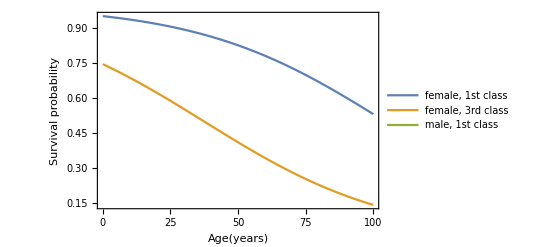

```mathematica
p[class_, age_, sex_] := c[{class, age, sex}, {"Probability", "survived"}];
Plot[{
p["1st", x, "female"], p["3rd", x, "female"], p["1st", x, "male"]. p["3rd", x, "male"]},
{x, 0, 100}, PlotLegends->
{"female, 1st class", "female, 3rd class", "male, 1st class", "male, 3rd class"},
Frame -> True, FrameLabel -> {"Age(years)", "Survival probability"}, Exclusions->None]
```

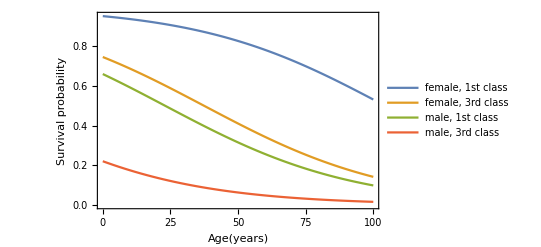

```mathematica
p[class_, age_, sex_] := c[{class, age, sex}, {"Probability", "survived"}];
Plot[{
p["1st", x, "female"], p["3rd", x, "female"], p["1st", x, "male"], p["3rd", x, "male"]},
{x, 0, 100}, PlotLegends->
{"female, 1st class", "female, 3rd class", "male, 1st class", "male, 3rd class"},
Frame -> True, FrameLabel -> {"Age(years)", "Survival probability"}, Exclusions->None]
```

```mathematica
c = Classify[ExampleData[{"MachineLearning", "MovieReview"}, "TrainingData"]]
```

ClassifierFunction[…]

```mathematica
c["the gorgeously elaborate continuation of \" the lord of the rings \" trilogy is so huge that a column of words cannot adequately describe co-writer/director peter jackson's expanded vision of j . r . r . tolkien's middle-earth . "]
```

positive

```mathematica
ClassifierMeasurements[c,ExampleData[{"MachineLearning","MovieReview"},"TestData"],"Accuracy"]
```

0.75125

ListPlot::prng: Value of option PlotRange -> {50} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

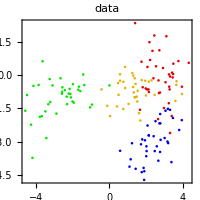

```mathematica
gaussian[μ_, σ_, n_] := RandomVariate[MultinormalDistribution[μ, {{σ, 0},{0, σ}}], n];
positions = {{4,2}, {-2,2},{0,-3},{3,0}};
sizes = {2, 1, 5, 0.5};
colors = {RGBColor[1,0,0],RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[1.,0.77,0.]};
nums = {100, 100, 50, 20};
clusters = MapThread[gaussian, {positions, sizes, nums}];
clusters=Table[RandomVariate[BinormalDistribution[RandomReal[{-3,3},2],RandomReal[{0.5,2},2],RandomReal[{0.2,0.8}]],RandomInteger[{30,40}]],{4}];
plot = ListPlot[clusters, PlotStyle-> Darker[colors, 0.1], ImageSize->200,
PlotRange->{{-5, 5}. {-5, 5}}, Frame -> True, AspectRatio->1, PlotLabel->"data"]
```

ListPlot::prng: Value of option PlotRange -> {50} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

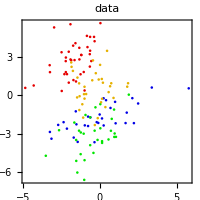

```mathematica
gaussian[μ_, σ_, n_] := RandomVariate[MultinormalDistribution[μ, {{σ, 0},{0, σ}}], n];
positions = {{4,2}, {-2,2},{0,-3},{3,0}};
sizes = {2, 1, 5, 0.5};
colors = {RGBColor[1,0,0],RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[1.,0.77,0.]};
nums = {100, 100, 50, 20};
clusters = MapThread[gaussian, {positions, sizes, nums}];
clusters=Table[RandomVariate[BinormalDistribution[RandomReal[{-3,3},2],RandomReal[{0.5,2},2],RandomReal[{0.2,0.8}]],RandomInteger[{30,40}]],{4}];
plot = ListPlot[clusters, PlotStyle-> Darker[colors, 0.1], ImageSize->200,
PlotRange->{{-5, 5}. {-5, 5}}, Frame -> True, AspectRatio->1, PlotLabel->"data"]
```

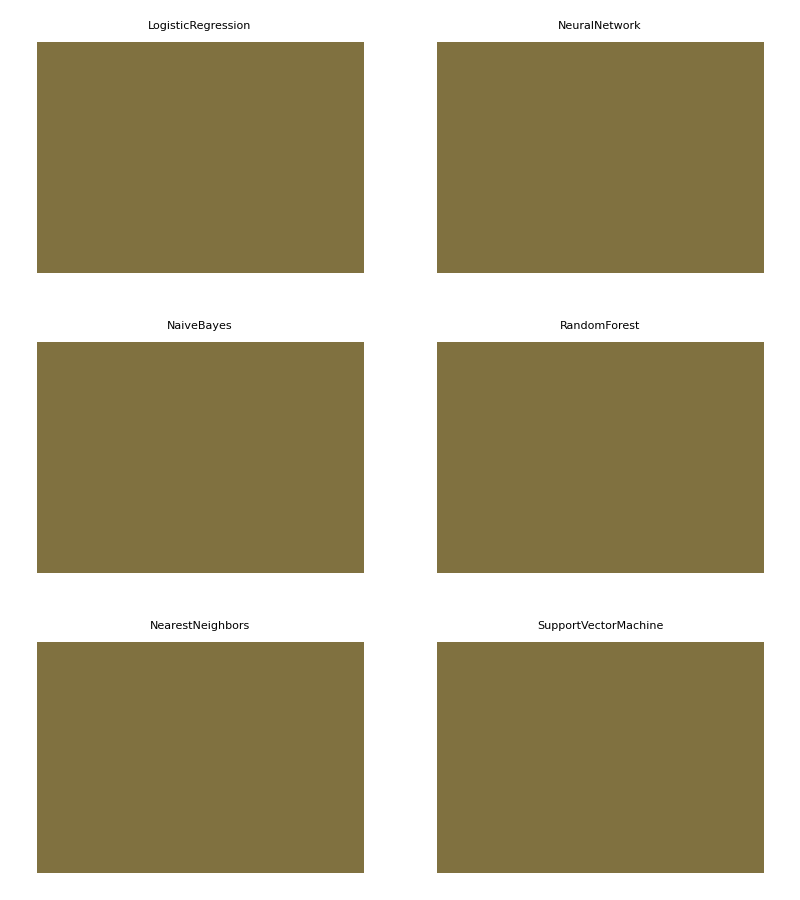

```mathematica
line = Range[-5, 5, 0.25];
points = Tuples[line, 2];
makecolormap[probs_] := Transpose @ Partition[Map[Blend[Keys[#]]&, probs],
Length[line]];
data = AssociationThread[colors, clusters];
methods = {"LogisticRegression", "NaiveBayes", "NearestNeighbors",
"NeuralNetwork", "RandomForest", "SupportVectorMachine"};
Table[
ArrayPlot[
makecolormap @ Classify[data, points, "Probabilities", Method->method],
PlotLabel->method, DataReversed->True, ImageSize -> 150], 
{method, methods}]~Multicolumn~2~Legended~plot
```

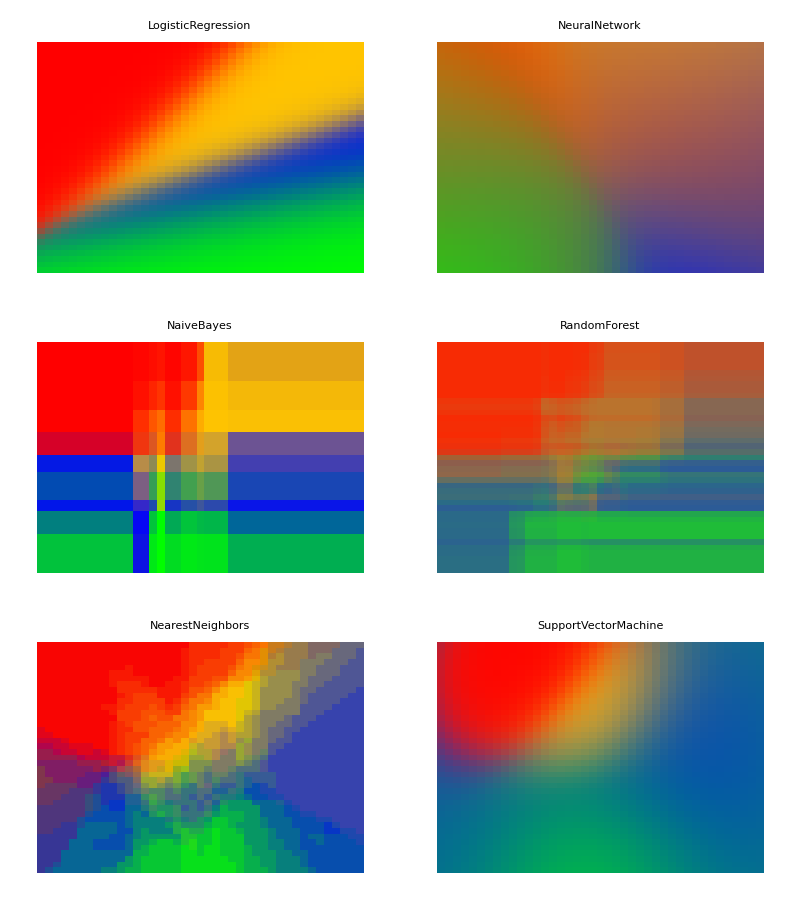

```mathematica
line=Range[-5,5,0.25];
points=Tuples[line,2];
makecolormap[probs_]:=Transpose@Partition[Map[Blend[Keys[#],Values[#]]&,probs],Length[line]];
data=AssociationThread[colors,clusters];
methods={"LogisticRegression","NaiveBayes","NearestNeighbors","NeuralNetwork","RandomForest","SupportVectorMachine"};
Table[ArrayPlot[makecolormap@Classify[data,points,"Probabilities",Method->method],PlotLabel->method,DataReversed->True,ImageSize->150],{method,methods}]~Multicolumn~2~Legended~plot
```